```mathematica
data=Import["/home/jose/Files/Complex Systems/proyecto/alltokens.csv", "Data"];
data[[1]]
Table[data[[i,j]],{i,10},{j,Length[data[[1]]]}] //TableView
```

{patient_id,frace,document_id,token_cancer}

patient_idfracedocument_idtoken_cancer217231quimioterapia2TREATMENT_NAME21723141 años2AGE217231Tumor maligno de mama2CANCER_CONCEPT217231acetato2DRUG217231goserelina2DRUG217231Politerapia Antineoplasica2TREATMENT_NAME136631CARCINOMA DE MAMA0CANCER_CONCEPT136631TAMOXIFENO0DRUG136631TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA0CANCER_CONCEPT

{}

Part::partd: Part specification data⟦2,3⟧ is longer than depth of object.

Part::partd: Part specification data⟦2,1⟧ is longer than depth of object.

Part::partd: Part specification data⟦2,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

97

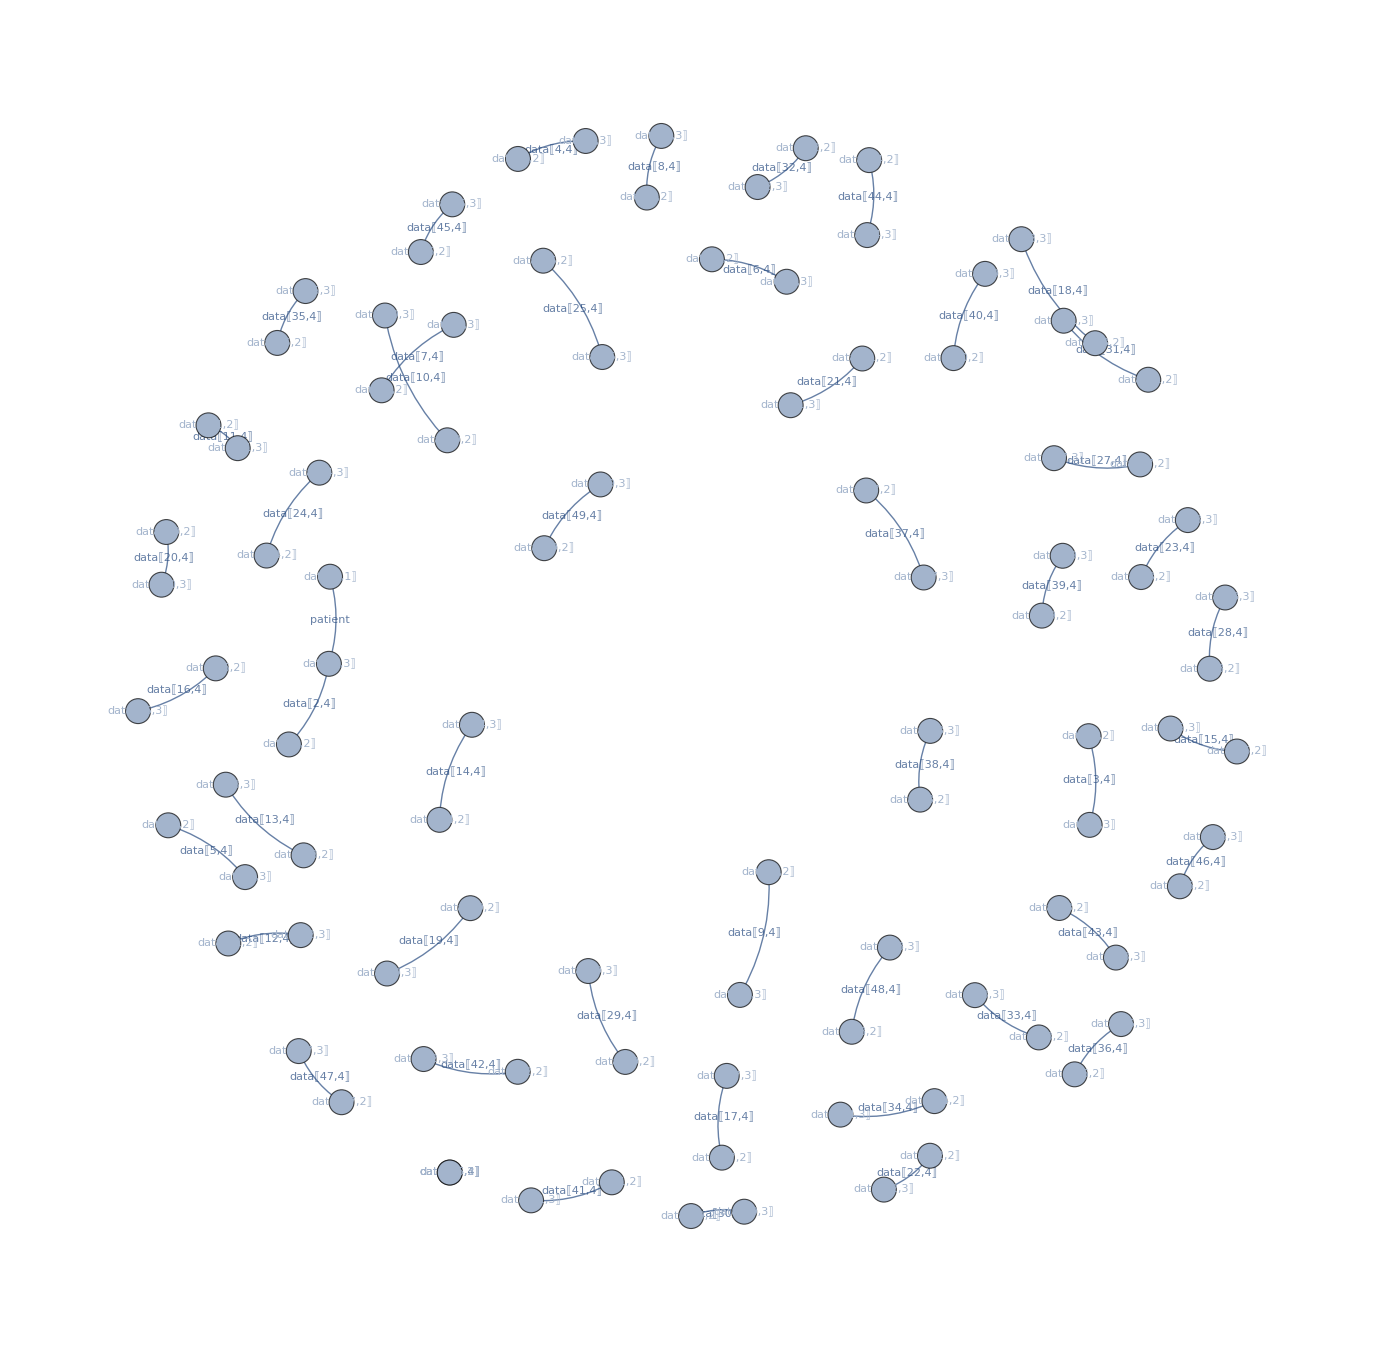

```mathematica
nodos = {}
GenerateGraph[data_]:= Module[{doc},
doc = data[[2,3]];
AppendTo[nodos,Labeled[data[[2,1]]<->data[[2,3]],"patient"]];
For[i=2,i<50,i++,
AppendTo[nodos,Labeled[data[[i,2]]<-> data[[i,3]],data[[i,4]]]];
If[doc != data[[i,3]],AppendTo[nodos,Labeled[data[[i,1]]<->data[[i,3]],"patient"]]];]]
GenerateGraph[data]
gp = Graph[nodos,VertexLabels->Placed[Automatic,Center],GraphLayout->"GravityEmbedding"];
VertexCount[gp]
gp
```